## CelleratorNetwork-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<xlr8r.m
```

xCellerator 0.95 (28-Feb-2014) loaded Tue 6 Jun 2017 11:43:39
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 11:43:42
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Generate 50 random vertices to use a Voronoi Centers

```mathematica
r:=RandomReal[{0,100}]; 
vertices=Table[{r,r}, {10}];
```

Use the Voronoi Centers to generate a tissue with 5 cells using the Bounded-Cell-Voronoi algorithm

```mathematica
w=BoundedCellVoronoi[vertices];
```

Show the tissue and the centers

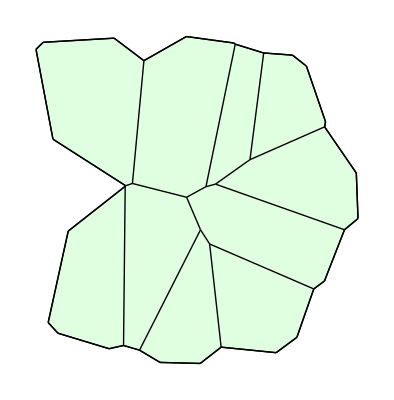

```mathematica
ShowTissue[w]
```

Define the Cellerator Network in a Single Cell

```mathematica
MyReactions = {{Underoverscript[X⟺XP, ZP, Z],MM[K,v,K,v]}, {Underoverscript[Y⟺YP, XP, X],MM[K,v,K,v]},
   {Underoverscript[Z⟺ZP, YP, Y],MM[K,v,K,v]}};
```

Generate the Reactions in the big network

```mathematica
bignet=CelleratorNetwork[w, "Reactions"-> MyReactions, "Diffusion"-> {{X,DX},{Y,DY},{Z,DZ}}];
```

10 Cells.

6 internal reactions in each cell.

60 intracellular reactions.

96 diffusion reactions.

156 total reactions.

```mathematica
bignet
```

{{(X[1]⟹XP[1])^Z[1],MM[K,v]},{(XP[1]⟹X[1])^ZP[1],MM[K,v]},{(Y[1]⟹YP[1])^X[1],MM[K,v]},{(YP[1]⟹Y[1])^XP[1],MM[K,v]},{(Z[1]⟹ZP[1])^Y[1],MM[K,v]},{(ZP[1]⟹Z[1])^YP[1],MM[K,v]},{(X[2]⟹XP[2])^Z[2],MM[K,v]},{(XP[2]⟹X[2])^ZP[2],MM[K,v]},{(Y[2]⟹YP[2])^X[2],MM[K,v]},{(YP[2]⟹Y[2])^XP[2],MM[K,v]},{(Z[2]⟹ZP[2])^Y[2],MM[K,v]},{(ZP[2]⟹Z[2])^YP[2],MM[K,v]},{(X[3]⟹XP[3])^Z[3],MM[K,v]},{(XP[3]⟹X[3])^ZP[3],MM[K,v]},{(Y[3]⟹YP[3])^X[3],MM[K,v]},{(YP[3]⟹Y[3])^XP[3],MM[K,v]},{(Z[3]⟹ZP[3])^Y[3],MM[K,v]},{(ZP[3]⟹Z[3])^YP[3],MM[K,v]},{(X[4]⟹XP[4])^Z[4],MM[K,v]},{(XP[4]⟹X[4])^ZP[4],MM[K,v]},{(Y[4]⟹YP[4])^X[4],MM[K,v]},{(YP[4]⟹Y[4])^XP[4],MM[K,v]},{(Z[4]⟹ZP[4])^Y[4],MM[K,v]},{(ZP[4]⟹Z[4])^YP[4],MM[K,v]},{(X[5]⟹XP[5])^Z[5],MM[K,v]},{(XP[5]⟹X[5])^ZP[5],MM[K,v]},{(Y[5]⟹YP[5])^X[5],MM[K,v]},{(YP[5]⟹Y[5])^XP[5],MM[K,v]},{(Z[5]⟹ZP[5])^Y[5],MM[K,v]},{(ZP[5]⟹Z[5])^YP[5],MM[K,v]},{(X[6]⟹XP[6])^Z[6],MM[K,v]},{(XP[6]⟹X[6])^ZP[6],MM[K,v]},{(Y[6]⟹YP[6])^X[6],MM[K,v]},{(YP[6]⟹Y[6])^XP[6],MM[K,v]},{(Z[6]⟹ZP[6])^Y[6],MM[K,v]},{(ZP[6]⟹Z[6])^YP[6],MM[K,v]},{(X[7]⟹XP[7])^Z[7],MM[K,v]},{(XP[7]⟹X[7])^ZP[7],MM[K,v]},{(Y[7]⟹YP[7])^X[7],MM[K,v]},{(YP[7]⟹Y[7])^XP[7],MM[K,v]},{(Z[7]⟹ZP[7])^Y[7],MM[K,v]},{(ZP[7]⟹Z[7])^YP[7],MM[K,v]},{(X[8]⟹XP[8])^Z[8],MM[K,v]},{(XP[8]⟹X[8])^ZP[8],MM[K,v]},{(Y[8]⟹YP[8])^X[8],MM[K,v]},{(YP[8]⟹Y[8])^XP[8],MM[K,v]},{(Z[8]⟹ZP[8])^Y[8],MM[K,v]},{(ZP[8]⟹Z[8])^YP[8],MM[K,v]},{(X[9]⟹XP[9])^Z[9],MM[K,v]},{(XP[9]⟹X[9])^ZP[9],MM[K,v]},{(Y[9]⟹YP[9])^X[9],MM[K,v]},{(YP[9]⟹Y[9])^XP[9],MM[K,v]},{(Z[9]⟹ZP[9])^Y[9],MM[K,v]},{(ZP[9]⟹Z[9])^YP[9],MM[K,v]},{(X[10]⟹XP[10])^Z[10],MM[K,v]},{(XP[10]⟹X[10])^ZP[10],MM[K,v]},{(Y[10]⟹YP[10])^X[10],MM[K,v]},{(YP[10]⟹Y[10])^XP[10],MM[K,v]},{(Z[10]⟹ZP[10])^Y[10],MM[K,v]},{(ZP[10]⟹Z[10])^YP[10],MM[K,v]},{X[1]⇄∅,0.0536565 DX,0.0536565 DX X[2][t]},{X[1]⇄∅,0.070695 DX,0.070695 DX X[6][t]},{X[2]⇄∅,0.0344698 DX,0.0344698 DX X[1][t]},{X[2]⇄∅,0.0578634 DX,0.0578634 DX X[4][t]},{X[2]⇄∅,0.017873 DX,0.017873 DX X[6][t]},{X[3]⇄∅,0.0146376 DX,0.0146376 DX X[4][t]},{X[3]⇄∅,0.00297169 DX,0.00297169 DX X[7][t]},{X[3]⇄∅,0.055863 DX,0.055863 DX X[8][t]},{X[3]⇄∅,0.0658679 DX,0.0658679 DX X[9][t]},{X[3]⇄∅,0.0231573 DX,0.0231573 DX X[10][t]},{X[4]⇄∅,0.0523643 DX,0.0523643 DX X[2][t]},{X[4]⇄∅,0.013517 DX,0.013517 DX X[3][t]},{X[4]⇄∅,0.043401 DX,0.043401 DX X[5][t]},{X[4]⇄∅,0.00377522 DX,0.00377522 DX X[6][t]},{X[4]⇄∅,0.00646483 DX,0.00646483 DX X[8][t]},{X[4]⇄∅,0.00844495 DX,0.00844495 DX X[10][t]},{X[5]⇄∅,0.0523856 DX,0.0523856 DX X[4][t]},{X[5]⇄∅,0.047876 DX,0.047876 DX X[8][t]},{X[6]⇄∅,0.0829854 DX,0.0829854 DX X[1][t]},{X[6]⇄∅,0.0326584 DX,0.0326584 DX X[2][t]},{X[6]⇄∅,0.00762266 DX,0.00762266 DX X[4][t]},{X[6]⇄∅,0.112259 DX,0.112259 DX X[10][t]},{X[7]⇄∅,0.00213209 DX,0.00213209 DX X[3][t]},{X[7]⇄∅,0.0366188 DX,0.0366188 DX X[10][t]},{X[8]⇄∅,0.0751992 DX,0.0751992 DX X[3][t]},{X[8]⇄∅,0.00942401 DX,0.00942401 DX X[4][t]},{X[8]⇄∅,0.0578208 DX,0.0578208 DX X[5][t]},{X[9]⇄∅,0.0622607 DX,0.0622607 DX X[3][t]},{X[10]⇄∅,0.0158012 DX,0.0158012 DX X[3][t]},{X[10]⇄∅,0.00624008 DX,0.00624008 DX X[4][t]},{X[10]⇄∅,0.0410818 DX,0.0410818 DX X[6][t]},{X[10]⇄∅,0.0348262 DX,0.0348262 DX X[7][t]},{Y[1]⇄∅,0.0536565 DY,0.0536565 DY Y[2][t]},{Y[1]⇄∅,0.070695 DY,0.070695 DY Y[6][t]},{Y[2]⇄∅,0.0344698 DY,0.0344698 DY Y[1][t]},{Y[2]⇄∅,0.0578634 DY,0.0578634 DY Y[4][t]},{Y[2]⇄∅,0.017873 DY,0.017873 DY Y[6][t]},{Y[3]⇄∅,0.0146376 DY,0.0146376 DY Y[4][t]},{Y[3]⇄∅,0.00297169 DY,0.00297169 DY Y[7][t]},{Y[3]⇄∅,0.055863 DY,0.055863 DY Y[8][t]},{Y[3]⇄∅,0.0658679 DY,0.0658679 DY Y[9][t]},{Y[3]⇄∅,0.0231573 DY,0.0231573 DY Y[10][t]},{Y[4]⇄∅,0.0523643 DY,0.0523643 DY Y[2][t]},{Y[4]⇄∅,0.013517 DY,0.013517 DY Y[3][t]},{Y[4]⇄∅,0.043401 DY,0.043401 DY Y[5][t]},{Y[4]⇄∅,0.00377522 DY,0.00377522 DY Y[6][t]},{Y[4]⇄∅,0.00646483 DY,0.00646483 DY Y[8][t]},{Y[4]⇄∅,0.00844495 DY,0.00844495 DY Y[10][t]},{Y[5]⇄∅,0.0523856 DY,0.0523856 DY Y[4][t]},{Y[5]⇄∅,0.047876 DY,0.047876 DY Y[8][t]},{Y[6]⇄∅,0.0829854 DY,0.0829854 DY Y[1][t]},{Y[6]⇄∅,0.0326584 DY,0.0326584 DY Y[2][t]},{Y[6]⇄∅,0.00762266 DY,0.00762266 DY Y[4][t]},{Y[6]⇄∅,0.112259 DY,0.112259 DY Y[10][t]},{Y[7]⇄∅,0.00213209 DY,0.00213209 DY Y[3][t]},{Y[7]⇄∅,0.0366188 DY,0.0366188 DY Y[10][t]},{Y[8]⇄∅,0.0751992 DY,0.0751992 DY Y[3][t]},{Y[8]⇄∅,0.00942401 DY,0.00942401 DY Y[4][t]},{Y[8]⇄∅,0.0578208 DY,0.0578208 DY Y[5][t]},{Y[9]⇄∅,0.0622607 DY,0.0622607 DY Y[3][t]},{Y[10]⇄∅,0.0158012 DY,0.0158012 DY Y[3][t]},{Y[10]⇄∅,0.00624008 DY,0.00624008 DY Y[4][t]},{Y[10]⇄∅,0.0410818 DY,0.0410818 DY Y[6][t]},{Y[10]⇄∅,0.0348262 DY,0.0348262 DY Y[7][t]},{Z[1]⇄∅,0.0536565 DZ,0.0536565 DZ Z[2][t]},{Z[1]⇄∅,0.070695 DZ,0.070695 DZ Z[6][t]},{Z[2]⇄∅,0.0344698 DZ,0.0344698 DZ Z[1][t]},{Z[2]⇄∅,0.0578634 DZ,0.0578634 DZ Z[4][t]},{Z[2]⇄∅,0.017873 DZ,0.017873 DZ Z[6][t]},{Z[3]⇄∅,0.0146376 DZ,0.0146376 DZ Z[4][t]},{Z[3]⇄∅,0.00297169 DZ,0.00297169 DZ Z[7][t]},{Z[3]⇄∅,0.055863 DZ,0.055863 DZ Z[8][t]},{Z[3]⇄∅,0.0658679 DZ,0.0658679 DZ Z[9][t]},{Z[3]⇄∅,0.0231573 DZ,0.0231573 DZ Z[10][t]},{Z[4]⇄∅,0.0523643 DZ,0.0523643 DZ Z[2][t]},{Z[4]⇄∅,0.013517 DZ,0.013517 DZ Z[3][t]},{Z[4]⇄∅,0.043401 DZ,0.043401 DZ Z[5][t]},{Z[4]⇄∅,0.00377522 DZ,0.00377522 DZ Z[6][t]},{Z[4]⇄∅,0.00646483 DZ,0.00646483 DZ Z[8][t]},{Z[4]⇄∅,0.00844495 DZ,0.00844495 DZ Z[10][t]},{Z[5]⇄∅,0.0523856 DZ,0.0523856 DZ Z[4][t]},{Z[5]⇄∅,0.047876 DZ,0.047876 DZ Z[8][t]},{Z[6]⇄∅,0.0829854 DZ,0.0829854 DZ Z[1][t]},{Z[6]⇄∅,0.0326584 DZ,0.0326584 DZ Z[2][t]},{Z[6]⇄∅,0.00762266 DZ,0.00762266 DZ Z[4][t]},{Z[6]⇄∅,0.112259 DZ,0.112259 DZ Z[10][t]},{Z[7]⇄∅,0.00213209 DZ,0.00213209 DZ Z[3][t]},{Z[7]⇄∅,0.0366188 DZ,0.0366188 DZ Z[10][t]},{Z[8]⇄∅,0.0751992 DZ,0.0751992 DZ Z[3][t]},{Z[8]⇄∅,0.00942401 DZ,0.00942401 DZ Z[4][t]},{Z[8]⇄∅,0.0578208 DZ,0.0578208 DZ Z[5][t]},{Z[9]⇄∅,0.0622607 DZ,0.0622607 DZ Z[3][t]},{Z[10]⇄∅,0.0158012 DZ,0.0158012 DZ Z[3][t]},{Z[10]⇄∅,0.00624008 DZ,0.00624008 DZ Z[4][t]},{Z[10]⇄∅,0.0410818 DZ,0.0410818 DZ Z[6][t]},{Z[10]⇄∅,0.0348262 DZ,0.0348262 DZ Z[7][t]}}

Define some random initial conditions

```mathematica
r:=RandomReal[{0,2}]; 
MyIC=Sort[Flatten[{X[#]-> r, Y[#]-> r, Z[#]-> r, XP[#]-> r, YP[#]-> r, ZP[#]-> r}&/@Range[10]]]
```

{X[1]→0.614195,X[2]→0.333269,X[3]→0.162655,X[4]→0.354538,X[5]→1.78931,X[6]→1.10617,X[7]→1.85935,X[8]→1.87085,X[9]→0.461503,X[10]→1.03692,XP[1]→1.61449,XP[2]→0.240366,XP[3]→1.87162,XP[4]→1.5163,XP[5]→1.14153,XP[6]→0.487757,XP[7]→0.0306488,XP[8]→1.37346,XP[9]→1.31021,XP[10]→0.329121,Y[1]→0.420789,Y[2]→1.49267,Y[3]→0.605915,Y[4]→0.531697,Y[5]→1.1567,Y[6]→0.201503,Y[7]→0.0559575,Y[8]→1.89293,Y[9]→1.30196,Y[10]→0.81693,YP[1]→1.2231,YP[2]→0.867451,YP[3]→1.47653,YP[4]→0.313165,YP[5]→1.3618,YP[6]→0.266775,YP[7]→1.68771,YP[8]→1.73812,YP[9]→0.800487,YP[10]→0.702129,Z[1]→1.63149,Z[2]→1.04219,Z[3]→1.23091,Z[4]→1.80826,Z[5]→1.03056,Z[6]→1.50225,Z[7]→1.69294,Z[8]→0.153864,Z[9]→1.60649,Z[10]→0.449156,ZP[1]→0.258716,ZP[2]→1.43376,ZP[3]→1.78195,ZP[4]→1.08907,ZP[5]→1.59928,ZP[6]→0.245405,ZP[7]→0.432012,ZP[8]→1.10319,ZP[9]→1.66901,ZP[10]→1.21259}

Define the Paraemters and run a single simulation

```mathematica
MyParameters = {v -> 1, K -> .5, DX-> 13, DY-> 15, DZ-> 11};
```

```mathematica
mysim = run[bignet, {0, 25}, rates->MyParameters, initialConditions-> MyIC];
```

Plot the results

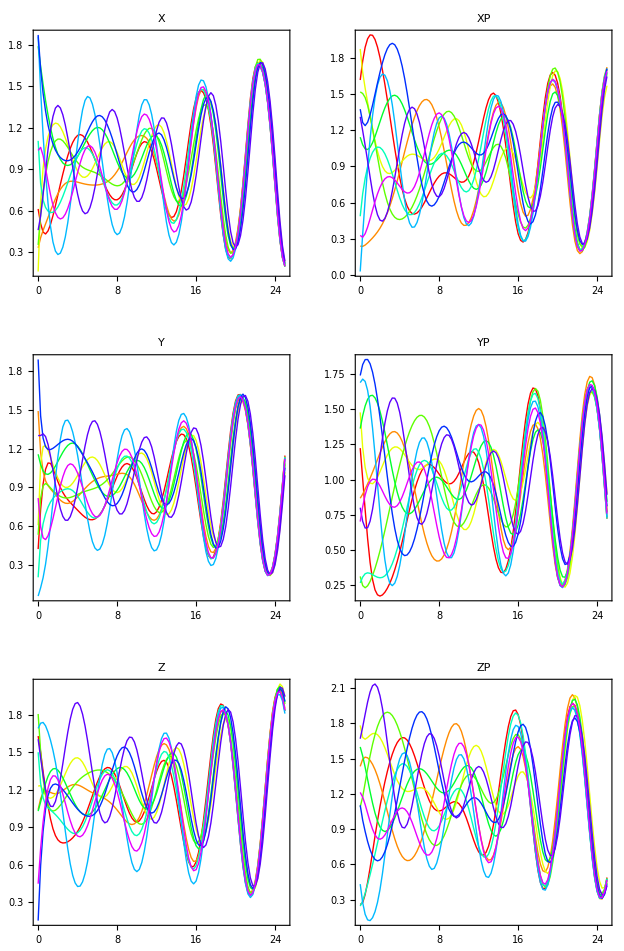

```mathematica
GraphicsGrid[Partition[SimPlot[mysim],2]]
```